```mathematica
trans:=(r1 - a1  Exp[I ϕ1])/(1-r1   a1  Exp[I ϕ1])       
ref:= (- t1 t2 √a1 Exp[I ϕ1/2])/(1-r1   a1  Exp[I ϕ1])
```

```mathematica
n:=3.45;
R1:=10 10^(-6);
R2:=10 10^(-6);
d1:= 2 Pi R1
d2:= 2 Pi R2
c := 299792458
λ:=1550 10^(-9); (* resonant wavelrngth *)
Q1:=1×10^5;
Q2:=1×10^6;
α1:=(2 Pi n)/(λ  Q1)
α2:=(2 Pi n)/(λ  Q2)
a1:= Exp[- α1 d1]
a2:= Exp[- α2 d2]
t1:=√(1-r1^2)
t2:=√(1-r2^2)
t3:=√(1-r3^2)
r1:= 0.997
r2:= 0.999
r3:= 0.999
```

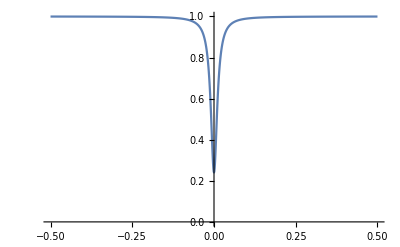

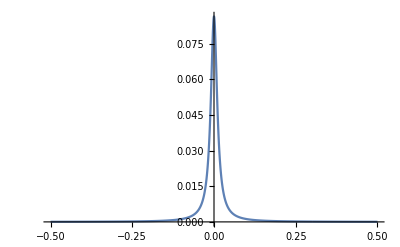

```mathematica
ϕ1min:=-0.5;
ϕ1max:=0.5;
transdata:=Table[{ϕ1,Abs[trans]^2},{ϕ1,ϕ1min, ϕ1max, 0.001}]
refdata:=Table[{ϕ1,Abs[ref]^2},{ϕ1,ϕ1min, ϕ1max, 0.0001}]
ListLinePlot[transdata,PlotRange->{0,1}]
ListLinePlot[refdata,PlotRange->All]
```

```mathematica
ϕeff := Pi + ϕ1 + 2ArcTan [(r1 Sin[ ϕ1])/(1-r1 Cos [ϕ1])]
```

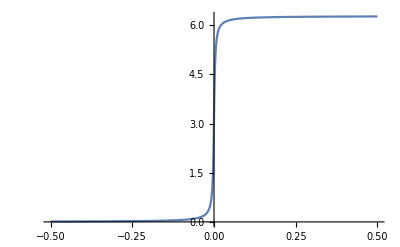

```mathematica
ϕ1min:=-0.5;
ϕ1max:=0.5;
transdata:=Table[{ϕ1,ϕeff},{ϕ1,ϕ1min, ϕ1max, 0.001}]
ListLinePlot[transdata,PlotRange->All]
```

```mathematica
dϕ := D[ϕeff, {ϕ1,1}]
vg := (n/c)+(n/c) (1+(2 ((0.997 Cos[ϕ1])/(1-0.997 Cos[ϕ1])-(0.994009 Sin[ϕ1]^2)/(1-0.997 Cos[ϕ1])^2))/(1+(0.994009 Sin[ϕ1]^2)/(1-0.997 Cos[ϕ1])^2))
```

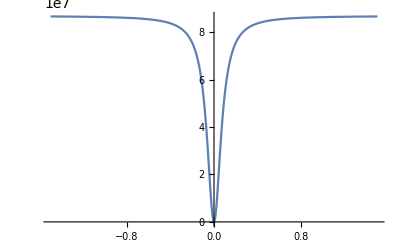

```mathematica
transdata:=Table[{ϕ1,1/ vg},{ϕ1,-1.5, 1.5, 0.001}]
ListLinePlot[transdata,PlotRange->All]
```